```mathematica
required: system of 2 quads and 1 payload
```

system elements :
quad 1 - given as system input. x,y coor. θ is not influential
quad 2  - given as system input. x,y coor. θ is not influential
payload (contrained to quads locations)

```mathematica
Quit[]
```

```mathematica
Needs["VariationalMethods`"]
```

kinematics :

```mathematica
prop2D={(Subscript[X, i]=({{Subscript[x, i][t]}, {Subscript[y, i][t]}, {0}}))//MatrixForm//TraditionalForm,
(Subscript[Imat, i]=({{Subscript[I, i,xx], 0, 0}, {0, Subscript[I, i,yy], 0}, {0, 0, Subscript[I, i,zz]}}))//MatrixForm//TraditionalForm,
Subscript[ω, i]=D[{0,0,Subscript[θ, i][t]},t]}
prop2D/.i->1
prop2D/.i->2
prop2D/.i->p
(Subscript[v, i]=D[Subscript[X, i],t])//MatrixForm//TraditionalForm
Subscript[v, i]/.i->1
Subscript[v, i]/.i->2
Subscript[v, i]/.i->p
```

{(x_i(t)
y_i(t)
0),(ⅈ_(i,xx) | 0 | 0
0 | ⅈ_(i,yy) | 0
0 | 0 | ⅈ_(i,zz)),{0,0,θ_i'[t]}}

{(x_1(t)
y_1(t)
0),(ⅈ_(1,xx) | 0 | 0
0 | ⅈ_(1,yy) | 0
0 | 0 | ⅈ_(1,zz)),{0,0,θ_1'[t]}}

{(x_2(t)
y_2(t)
0),(ⅈ_(2,xx) | 0 | 0
0 | ⅈ_(2,yy) | 0
0 | 0 | ⅈ_(2,zz)),{0,0,θ_2'[t]}}

{(x_p(t)
y_p(t)
0),(ⅈ_(p,xx) | 0 | 0
0 | ⅈ_(p,yy) | 0
0 | 0 | ⅈ_(p,zz)),{0,0,θ_p'[t]}}

(x_i'(t)
y_i'(t)
0)

{{x_1'[t]},{y_1'[t]},{0}}

{{x_2'[t]},{y_2'[t]},{0}}

{{x_p'[t]},{y_p'[t]},{0}}

```mathematica
dispSimp = {a_[t]->a,Cos[a_]->c[a],Sin[a_]->s[a],Subscript[ⅈ, i_,zz]->Subscript[I, i]};
{(Rp2I=RotationMatrix[Subscript[θ, p][t]])//MatrixForm,
x1dotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->1,
x2dotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->2,
IωSqr1=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->1,
IωSqr2=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->2,
xpdotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->p,
IωSqrp=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->p,
Subscript[r, 1][t]=({{Subscript[x, 1][t]}, {Subscript[y, 1][t]}})-(({{Subscript[x, p][t]}, {Subscript[y, p][t]}})+Rp2I.{-Subscript[l, p]/2,Subscript[h, p]/2}),
Subscript[r, 2][t]=({{Subscript[x, 2][t]}, {Subscript[y, 2][t]}})-(({{Subscript[x, p][t]}, {Subscript[y, p][t]}})+Rp2I.{Subscript[l, p]/2,Subscript[h, p]/2}),
Subscript[Δ, 1]=√((Subscript[r, 1][t][[1]])^2+(Subscript[r, 1][t][[2]])^2)-Subscript[L0, 1],

Subscript[Δ, 2]=√((Subscript[r, 2][t][[1]])^2+(Subscript[r, 2][t][[2]])^2)-Subscript[L0, 2]};
(T=1/2 Subscript[m, 1] x1dotSqr+1/2 IωSqr1+1/2 Subscript[m, 2] x2dotSqr+1/2 IωSqr2+1/2 Subscript[m, p] xpdotSqr+1/2 IωSqrp);
(*Subscript[r, i]=Subscript[l, i]+Δl*)
V=Subscript[m, 1] g(Subscript[X, i][[2]]/.i->1)+Subscript[m, 2] g(Subscript[X, i][[2]]/.i->2)+Subscript[m, p] g(Subscript[X, i][[2]]/.i->p)+1/2 Subscript[k, 1] Subscript[Δ, 1]^2+1/2 Subscript[k, 2] Subscript[Δ, 2]^2;
L=(T-V)[[1]] (*Subscript[T, quad#1]+Subscript[T, quad#2]+Subscript[T, payload] - (Subscript[V, quad#1]+Subscript[V, quad#2]+Subscript[V, payload]+Subscript[V, spring#1]+Subscript[V, spring#2])*)
```

-g m_1 y_1[t]-g m_2 y_2[t]-1/2 k_1 (-L0_1+√((1/2 Sin[θ_p[t]] h_p+1/2 Cos[θ_p[t]] l_p+x_1[t]-x_p[t])^2+(-1/2 Cos[θ_p[t]] h_p+1/2 Sin[θ_p[t]] l_p+y_1[t]-y_p[t])^2))^2-1/2 k_2 (-L0_2+√((1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+(-1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p+y_2[t]-y_p[t])^2))^2-g m_p y_p[t]+1/2 m_1 (x_1'[t]^2+y_1'[t]^2)+1/2 m_2 (x_2'[t]^2+y_2'[t]^2)+1/2 m_p (x_p'[t]^2+y_p'[t]^2)+1/2 ⅈ_(1,zz) θ_1'[t]^2+1/2 ⅈ_(2,zz) θ_2'[t]^2+1/2 ⅈ_(p,zz) θ_p'[t]^2

```mathematica
L//.dispSimp//TraditionalForm
```

-1/2 k_1 (√((1/2 l_p c(θ_p)+1/2 h_p s(θ_p)-x_p+x_1)^2+(-1/2 h_p c(θ_p)+1/2 l_p s(θ_p)-y_p+y_1)^2)-L0_1)^2-1/2 k_2 (√((-1/2 l_p c(θ_p)+1/2 h_p s(θ_p)-x_p+x_2)^2+(-1/2 h_p c(θ_p)-1/2 l_p s(θ_p)-y_p+y_2)^2)-L0_2)^2-g m_p y_p-g m_1 y_1-g m_2 y_2+1/2 ⅈ_1 (θ_1')^2+1/2 ⅈ_2 (θ_2')^2+1/2 m_p ((x_p')^2+(y_p')^2)+1/2 m_1 ((x_1')^2+(y_1')^2)+1/2 m_2 ((x_2')^2+(y_2')^2)+1/2 ⅈ_p (θ_p')^2

```mathematica
(quadEqNominal=EulerEquations[L,{(*Subscript[x, 1][t],Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[θ, 2][t],*)Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Simplify)//MatrixForm//TraditionalForm
```

((k_1 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p x_p''(t)
(k_1 (-1/2 h_p cos(θ_p(t))+1/2 l_p sin(θ_p(t))-y_p(t)+y_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (-1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))-y_p(t)+y_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p (g+y_p''(t))
ⅈ_(p,zz) θ_p''(t)+(k_1 (h_p (x_1(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_1(t)-y_p(t)) sin(θ_p(t)))+l_p (x_1(t) (-sin(θ_p(t)))+x_p(t) sin(θ_p(t))+(y_1(t)-y_p(t)) cos(θ_p(t)))) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (h_p (x_2(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_2(t)-y_p(t)) sin(θ_p(t)))+l_p (x_2(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_2(t)) cos(θ_p(t)))) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(2 √((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==0)

```mathematica
terms2={
 (Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+2 Subscript[x, 1][t]-2 Subscript[x, p][t])^1->(2 r1x),(-1/2 Cos[Subscript[θ, p][t]] Subscript[h, p]+1/2 Sin[Subscript[θ, p][t]] Subscript[l, p]+Subscript[y, 1][t]-Subscript[y, p][t])^1->r1y,
1/2 Cos[Subscript[θ, p][t]] Subscript[h, p]-1/2 Sin[Subscript[θ, p][t]] Subscript[l, p]-Subscript[y, 1][t]+Subscript[y, p][t]->-r1y,
(1/2 Sin[Subscript[θ, p][t]] Subscript[h, p]-1/2 Cos[Subscript[θ, p][t]] Subscript[l, p]+Subscript[x, 2][t]-Subscript[x, p][t])^1->r2x, (-1/2 Cos[Subscript[θ, p][t]] Subscript[h, p]-1/2 Sin[Subscript[θ, p][t]] Subscript[l, p]+Subscript[y, 2][t]-Subscript[y, p][t])^1->r2y,
Cos[Subscript[θ, p][t]] Subscript[h, p]+Sin[Subscript[θ, p][t]] Subscript[l, p]-2 Subscript[y, 2][t]+2 Subscript[y, p][t]->(-2 r2y),
Subscript[l, p] (-Sin[Subscript[θ, p][t]] Subscript[x, 1][t]+Sin[Subscript[θ, p][t]] Subscript[x, p][t]+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))->dr1,
Subscript[h, p] (Cos[Subscript[θ, p][t]] Subscript[x, 1][t]-Cos[Subscript[θ, p][t]] Subscript[x, p][t]+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))->dr2,
Subscript[h, p] (Cos[Subscript[θ, p][t]] Subscript[x, 2][t]-Cos[Subscript[θ, p][t]] Subscript[x, p][t]+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))->dr4,
Subscript[l, p] (Sin[Subscript[θ, p][t]] Subscript[x, 2][t]-Sin[Subscript[θ, p][t]] Subscript[x, p][t]+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))->dr3
};
```

```mathematica
(simpStep1=(quadEqNominal(*//Simplify*))/.terms2)(*//.dispSimp*)(*//Simplify*)//MatrixForm(*//TraditionalForm*)
```

((r1x k_1 (√(r1x^2+r1y^2)-L0_1))/(√(r1x^2+r1y^2))+(r2x k_2 (√(r2x^2+r2y^2)-L0_2))/(√(r2x^2+r2y^2))==m_p x_p''[t]
(r1y k_1 (√(r1x^2+r1y^2)-L0_1))/(√(r1x^2+r1y^2))+(r2y k_2 (√(r2x^2+r2y^2)-L0_2))/(√(r2x^2+r2y^2))==m_p (g+y_p''[t])
((dr1+dr2) k_1 (√(r1x^2+r1y^2)-L0_1))/(2 √(r1x^2+r1y^2))+((dr3+dr4) k_2 (√(r2x^2+r2y^2)-L0_2))/(2 √(r2x^2+r2y^2))+ⅈ_(p,zz) θ_p''[t]==0)

```mathematica
terms3={
√(r1x^2+r1y^2)->a,
√(r2x^2+r2y^2)->b,
(dr1+dr2)->(2c1),
(dr3+dr4)->(2 c2),
r1x^2+r1y^2->a^2,r2x^2+r2y^2->b^2,
√(a^2)->a,√(b^2)->b}
```

{√(r1x^2+r1y^2)→a,√(r2x^2+r2y^2)→b,dr1+dr2→2 c1,dr3+dr4→2 c2,r1x^2+r1y^2→a^2,r2x^2+r2y^2→b^2,√(a^2)→a,√(b^2)→b}

```mathematica
(*simpStep1//InputForm*)
```

{(r1x*Subscript[k, 1]*(Sqrt[r1x^2 + r1y^2] - Subscript[L0, 1]))/Sqrt[r1x^2 + r1y^2] + (r2x*Subscript[k, 2]*(Sqrt[r2x^2 + r2y^2] - Subscript[L0, 2]))/
    Sqrt[r2x^2 + r2y^2] == Subscript[m, p]*Derivative[2][Subscript[x, p]][t], 
 (r1y*Subscript[k, 1]*(Sqrt[r1x^2 + r1y^2] - Subscript[L0, 1]))/Sqrt[r1x^2 + r1y^2] + (r2y*Subscript[k, 2]*(Sqrt[r2x^2 + r2y^2] - Subscript[L0, 2]))/
    Sqrt[r2x^2 + r2y^2] == Subscript[m, p]*(g + Derivative[2][Subscript[y, p]][t]), 
 ((dr1 + dr2)*Subscript[k, 1]*(Sqrt[r1x^2 + r1y^2] - Subscript[L0, 1]))/(2*Sqrt[r1x^2 + r1y^2]) + 
   ((dr3 + dr4)*Subscript[k, 2]*(Sqrt[r2x^2 + r2y^2] - Subscript[L0, 2]))/(2*Sqrt[r2x^2 + r2y^2]) + 
   Subscript[I, p, zz]*Derivative[2][Subscript[θ, p]][t] == 0}

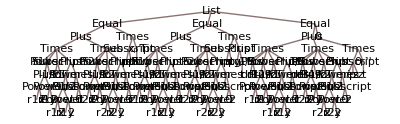

```mathematica
(*simpStep1//TreeForm*)
```

```mathematica
(simpStep2=(simpStep1//.terms3)//Simplify)//MatrixForm(*//TraditionalForm*)
```

((r1x k_1 (a-L0_1))/(√(a^2))+(r2x k_2 (b-L0_2))/(√(b^2))==m_p x_p''[t]
(r1y k_1 (a-L0_1))/(√(a^2))+(r2y k_2 (b-L0_2))/(√(b^2))==m_p (g+y_p''[t])
(c1 k_1 (a-L0_1))/(√(a^2))+(c2 k_2 (b-L0_2))/(√(b^2))+ⅈ_(p,zz) θ_p''[t]==0)

```mathematica
(simpStep3=Map[Map[Times[#,a b ]&,#]&,simpStep2]//Expand//Simplify)//MatrixForm
```

((√(a^2) b^2 r1x k_1 (a-L0_1)+a^2 √(b^2) r2x k_2 (b-L0_2))/(a b)==a b m_p x_p''[t]
(√(a^2) b^2 r1y k_1 (a-L0_1)+a^2 √(b^2) r2y k_2 (b-L0_2))/(a b)==a b m_p (g+y_p''[t])
(√(a^2) b^2 c1 k_1 (a-L0_1)+a^2 (√(b^2) c2 k_2 (b-L0_2)+b^2 ⅈ_(p,zz) θ_p''[t]))/(a b)==0)

```mathematica
simpStep3//.dispSimp//Expand//MatrixForm//TraditionalForm
```

(-(√(a^2) b k_1 L0_1 r1x)/a+√(a^2) b k_1 r1x-(a √(b^2) k_2 L0_2 r2x)/b+a √(b^2) k_2 r2x==a b m_p x_p''
-(√(a^2) b k_1 L0_1 r1y)/a+√(a^2) b k_1 r1y-(a √(b^2) k_2 L0_2 r2y)/b+a √(b^2) k_2 r2y==a b g m_p+a b m_p y_p''
-(√(a^2) b c1 k_1 L0_1)/a+√(a^2) b c1 k_1-(a √(b^2) c2 k_2 L0_2)/b+a √(b^2) c2 k_2+a b ⅈ_p θ_p''==0)

```mathematica
(simpStep4= Subscript[k, 1] b(a-Subscript[L0, 1])( {{r1x}, {r1y}, {c1}})+Subscript[k, 2] a(b-Subscript[L0, 1])( {{r2x}, {r2y}, {c2}})+({{0}, {-Subscript[m, p]g a b}, {0}})-a b ({{Subscript[m, p], 0, 0}, {0, Subscript[m, p], 0}, {0, 0, -Subscript[I, p]}}).({{Subscript[x, p]''[t]}, {Subscript[y, p]''[t]}, {Subscript[θ, p]''[t]}})-({{0}, {0}, {0}}))//MatrixForm
```

(b r1x k_1 (a-L0_1)+a r2x k_2 (b-L0_1)-a b m_p x_p''[t]
b r1y k_1 (a-L0_1)+a r2y k_2 (b-L0_1)-a b g m_p-a b m_p y_p''[t]
b c1 k_1 (a-L0_1)+a c2 k_2 (b-L0_1)+a b ⅈ_p θ_p''[t])

```mathematica
terms2//.dispSimp//MatrixForm//TraditionalForm
terms3//.dispSimp//MatrixForm//TraditionalForm
```

(l_p c(θ_p)+h_p s(θ_p)-2 x_p+2 x_1→2 r1x
-1/2 h_p c(θ_p)+1/2 l_p s(θ_p)-y_p+y_1→r1y
1/2 h_p c(θ_p)-1/2 l_p s(θ_p)+y_p-y_1→-r1y
-1/2 l_p c(θ_p)+1/2 h_p s(θ_p)-x_p+x_2→r2x
-1/2 h_p c(θ_p)-1/2 l_p s(θ_p)-y_p+y_2→r2y
h_p c(θ_p)+l_p s(θ_p)+2 y_p-2 y_2→-2 r2y
l_p ((y_1-y_p) c(θ_p)+x_1 (-s(θ_p))+x_p s(θ_p))→dr1
h_p (x_1 c(θ_p)-x_p c(θ_p)+(y_1-y_p) s(θ_p))→dr2
h_p (x_2 c(θ_p)-x_p c(θ_p)+(y_2-y_p) s(θ_p))→dr4
l_p ((y_p-y_2) c(θ_p)+x_2 s(θ_p)-x_p s(θ_p))→dr3)

(√(r1x^2+r1y^2)→a
√(r2x^2+r2y^2)→b
dr1+dr2→2 c1
dr3+dr4→2 c2
r1x^2+r1y^2→a^2
r2x^2+r2y^2→b^2
√(a^2)→a
√(b^2)→b)

```mathematica
(*Subscript[x, p],Subscript[y, p],Subscript[θ, p]=f(Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[k, 1],Subscript[k, 2],Subscript[l, p],Subscript[h, p])*)
```

```mathematica
non-conver forces:
aerodynamic =  f(OverDot[Subscript[x, p]],OverDot[Subscript[y, p]],Subscript[θ, p], Subscript[w, x],Subscript[w, y]) , w for wind components. = f(Subscript[relV, x],Subscript[relV, y]) , relV is relative to air 
dumping = f(OverDot[Subscript[l, i]])=f(OverDot[Subscript[x, i]],OverDot[Subscript[y, i]],OverDot[Subscript[x, p]],OverDot[Subscript[y, p]])
```

non dim the full equations

```mathematica
quadEqNominal/.terms2(*/.terms3*)//MatrixForm
```

((r1x k_1 (√(r1x^2+r1y^2)-L0_1))/(√(r1x^2+r1y^2))+(r2x k_2 (√(r2x^2+r2y^2)-L0_2))/(√(r2x^2+r2y^2))==m_p x_p''[t]
(r1y k_1 (√(r1x^2+r1y^2)-L0_1))/(√(r1x^2+r1y^2))+(r2y k_2 (√(r2x^2+r2y^2)-L0_2))/(√(r2x^2+r2y^2))==m_p (g+y_p''[t])
((dr1+dr2) k_1 (√(r1x^2+r1y^2)-L0_1))/(2 √(r1x^2+r1y^2))+((dr3+dr4) k_2 (√(r2x^2+r2y^2)-L0_2))/(2 √(r2x^2+r2y^2))+ⅈ_(p,zz) θ_p''[t]==0)

```mathematica
(smallEqs=quadEqNominal/.terms2/.terms3)//MatrixForm
```

((r1x k_1 (a-L0_1))/(√(a^2))+(r2x k_2 (b-L0_2))/(√(b^2))==m_p x_p''[t]
(r1y k_1 (a-L0_1))/(√(a^2))+(r2y k_2 (b-L0_2))/(√(b^2))==m_p (g+y_p''[t])
(c1 k_1 (a-L0_1))/(√(a^2))+(c2 k_2 (b-L0_2))/(√(b^2))+ⅈ_(p,zz) θ_p''[t]==0)

```mathematica
(*(NonDimEq=Map[Map[Times[#,1/(Subscript[m, p] Subscript[ω, s]^2 Subscript[L0, 1])]&,#]&,(*simpStep1*)smallEqs](*//Expand*)//FullSimplify)//MatrixForm*)
```

NonDimEq manually settings the terms:

```mathematica
OverTilde[Subscript[y, p]][t]=Subscript[y, p][t] /Subscript[L0, 1]  or any other of the lengths varialbes (Subscript[x, p],r1x,r1y,r2x,r2y,Subscript[h, p],Subscript[l, p])
t=τ/Subscript[ω, s]
Subscript[ω, s]^2=(Subscript[k, 1]/Subscript[m, p])[g/l=1/s^2]
A is non-dimentional  form of 'a'
B is non-dimentional  form of 'b'
```

```mathematica
(NonDimEq={Subscript[k, 1]/Subscript[m, p] (1-1/A Subscript[L0, 1]/Subscript[L0, 1])r1x Subscript[L0, 1]+Subscript[k, 2]/Subscript[k, 1] Subscript[k, 1]/Subscript[m, p]  (1-1/B Subscript[L0, 2]/Subscript[L0, 1])r2x Subscript[L0, 1]==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[x, p]''[t],Subscript[k, 1]/Subscript[m, p] (1-1/A Subscript[L0, 1]/Subscript[L0, 1])r1y Subscript[L0, 1]+Subscript[k, 2]/Subscript[k, 1] Subscript[k, 1]/Subscript[m, p]  (1-1/B Subscript[L0, 2]/Subscript[L0, 1])r2y Subscript[L0, 1]-g==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[y, p]''[t],Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) (1-1/A Subscript[L0, 1]/Subscript[L0, 1])Subscript[c, 1] Subscript[L0, 1]^2+Subscript[k, 2]/Subscript[k, 1] Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) (1-1/B Subscript[L0, 2]/Subscript[L0, 1])Subscript[c, 2] Subscript[L0, 1]^2==Subscript[ω, s]^2 Subscript[θ, p]''[t]})//Flatten//MatrixForm//TraditionalForm
```

(((1-1/A) k_1 L0_1 r1x)/m_p+(k_2 L0_1 r2x (1-L0_2/(B L0_1)))/m_p==L0_1 ω_s^2 x_p''(t)
((1-1/A) k_1 L0_1 r1y)/m_p+(k_2 L0_1 r2y (1-L0_2/(B L0_1)))/m_p-g==L0_1 ω_s^2 y_p''(t)
-((1-1/A) c_1 k_1 L0_1^2)/(ⅈ_(p,zz))-(c_2 k_2 L0_1^2 (1-L0_2/(B L0_1)))/(ⅈ_(p,zz))==ω_s^2 θ_p''(t))

```mathematica
(*terms4={(*1- Subscript[L0, 1]/a->A,
1-Subscript[L0, 2]/b->B,*)
Subscript[k, 2]/Subscript[k, 1]->k,(*=Subscript[k, ratio],*)
g/Subscript[L0, 1] 1/Subscript[ω, s]^2->γ,
(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p,zz] Subscript[ω, s]^2)->Ε,
Subscript[k, 1]/Subscript[m, p]->Subscript[ω, s]^2
}*)
```

```mathematica
(*Subscript[Delta, Equilibrium]=(Subscript[m, p] g)/Subscript[k, i]*)
```

```mathematica
(*g/Subscript[L0, 1] 1/Subscript[ω, s]^2==g 1/Subscript[L0, 1] 1/Subscript[k, 1] Subscript[m, p][m/s^2 1/m 1/(kg/s^2)kg]
(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p,zz] Subscript[ω, s]^2)==(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p,zz] Subscript[k, 1])Subscript[m, p][(m^2 kg)/(kg m^2)]*)
```

```mathematica
greekTerms={
Subscript[k, 2]/Subscript[k, 1]->κ,
Subscript[L0, 2]/Subscript[L0, 1]->ℒ,
Subscript[k, 1]/Subscript[m, p]->Subscript[ω, s]^2,
(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p](=(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2))->α,
g/(Subscript[L0, 1] Subscript[ω, s]^2)(=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))->γ
}
```

```mathematica
(NonDimEq={
Subscript[ω, s]^2 Subscript[L0, 1](1-1/A)r1x +κ Subscript[ω, s]^2  Subscript[L0, 1](1-1/B ℒ)r2x ==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[x, p]''[t],
Subscript[ω, s]^2 Subscript[L0, 1](1-1/A)r1y +κ Subscript[ω, s]^2  Subscript[L0, 1](1-1/B ℒ)r2y -g/(Subscript[L0, 1] Subscript[ω, s]^2)Subscript[L0, 1] Subscript[ω, s]^2==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[y, p]''[t],
Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) Subscript[L0, 1]^2/Subscript[ω, s]^2 Subscript[ω, s]^2(1-1/A)Subscript[c, 1] +κ Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) Subscript[L0, 1]^2/Subscript[ω, s]^2 Subscript[ω, s]^2(1-1/B ℒ)Subscript[c, 2]==Subscript[ω, s]^2 Subscript[θ, p]''[t]
})//Flatten//MatrixForm//TraditionalForm
```

((1-1/A) L0_1 r1x ω_s^2+κ L0_1 r2x (1-ℒ/B) ω_s^2==L0_1 ω_s^2 x_p''(t)
(1-1/A) L0_1 r1y ω_s^2+κ L0_1 r2y (1-ℒ/B) ω_s^2-g==L0_1 ω_s^2 y_p''(t)
-((1-1/A) c_1 k_1 L0_1^2)/(ⅈ_(p,zz))-(c_2 κ k_1 L0_1^2 (1-ℒ/B))/(ⅈ_(p,zz))==ω_s^2 θ_p''(t))

```mathematica
using 'greekTerms' list:
```

```mathematica
(NonDimEq={
Subscript[x, p]''[t]==(1-1/A)r1x +κ (1-1/B ℒ)r2x ,
Subscript[y, p]''[t]==(1-1/A)r1y +κ (1-1/B ℒ)r2y -γ,
Subscript[θ, p]''[t]==-α ((1-1/A)Subscript[c, 1] +κ  (1-1/B ℒ)Subscript[c, 2])
})//Flatten//MatrixForm//TraditionalForm
```

(x_p''(t)==(1-1/A) r1x+κ r2x (1-ℒ/B)
y_p''(t)==(1-1/A) r1y+κ r2y (1-ℒ/B)-γ
θ_p''(t)==-α ((1-1/A) c_1+c_2 κ (1-ℒ/B)))

```mathematica
Subscript[𝒱, 1]=({{r1x}, {r1y}, {Subscript[c, 1]}})(Subscript[x, 1],Subscript[x, p],θ_(p,..))
Subscript[𝒱, 2]=({{r2x}, {r2y}, {Subscript[c, 2]}})
```

```mathematica
𝒳^(..)=({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)Subscript[𝒱, 1]+κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)Subscript[𝒱, 2]-({{0}, {γ}, {0}})
```

```mathematica
terms2
terms3
```

{Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+2 x_1[t]-2 x_p[t]→2 r1x,-1/2 Cos[θ_p[t]] h_p+1/2 Sin[θ_p[t]] l_p+y_1[t]-y_p[t]→r1y,1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p-y_1[t]+y_p[t]→-r1y,1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t]→r2x,-1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p+y_2[t]-y_p[t]→r2y,Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p-2 y_2[t]+2 y_p[t]→-2 r2y,l_p (-Sin[θ_p[t]] x_1[t]+Sin[θ_p[t]] x_p[t]+Cos[θ_p[t]] (y_1[t]-y_p[t]))→dr1,h_p (Cos[θ_p[t]] x_1[t]-Cos[θ_p[t]] x_p[t]+Sin[θ_p[t]] (y_1[t]-y_p[t]))→dr2,h_p (Cos[θ_p[t]] x_2[t]-Cos[θ_p[t]] x_p[t]+Sin[θ_p[t]] (y_2[t]-y_p[t]))→dr4,l_p (Sin[θ_p[t]] x_2[t]-Sin[θ_p[t]] x_p[t]+Cos[θ_p[t]] (-y_2[t]+y_p[t]))→dr3}

{√(r1x^2+r1y^2)→a,√(r2x^2+r2y^2)→b,dr1+dr2→2 c1,dr3+dr4→2 c2,r1x^2+r1y^2→a^2,r2x^2+r2y^2→b^2,√(a^2)→a,√(b^2)→b}

```mathematica
𝒳=({{Subscript[x, p][t]}, {Subscript[y, p][t]}, {Subscript[θ, p][t]}})(*//Flatten*)
greekTermsSymetricCase={
(*Subscript[k, 2]/Subscript[k, 1]->*)κ->1,
(*Subscript[L0, 2]/Subscript[L0, 1]->*)ℒ->1
}
greekTermsGeneral={
(*Subscript[k, 2]/Subscript[k, 1]->*)κ->1,
(*Subscript[L0, 2]/Subscript[L0, 1]->*)ℒ->1,
(*Subscript[k, 1]/Subscript[m, p]->*)Subscript[ω, s]^2->1,
(*(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p](=(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2))->*)α->1,
(*g/(Subscript[L0, 1] Subscript[ω, s]^2)(=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))-> *)γ->1 (* make sure it is not over-determined constant *)

}
(* already here : replacing all former Subscript[h, p],Subscript[l, p] with new 2 Subscript[h, p],2 Subscript[l, p]*)
A(*->√(r1x^2+r1y^2)*)=√((Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 1][t]-Subscript[x, p][t]))^2+(- Cos[Subscript[θ, p][t]] Subscript[h, p]+ Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 1][t]-Subscript[y, p][t]))^2)

B(*->√(r2x^2+r2y^2)*)=√((Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 2][t]-Subscript[x, p][t]))^2+(- Cos[Subscript[θ, p][t]] Subscript[h, p]- Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 2][t]-Subscript[y, p][t]))^2)
(*Subscript[c, 1](*->dr1+dr2*)=Subscript[l, p] (-Sin[Subscript[θ, p][t]] (Subscript[x, 1][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 1][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))
Subscript[c, 2](*->dr3+dr4*)=Subscript[l, p] (Sin[Subscript[θ, p][t]] (Subscript[x, 2][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 2][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))*)
Subscript[𝒱, 1](*=({{r1x}, {r1y}, {Subscript[c, 1]}})*)=({{(Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 1][t]-Subscript[x, p][t]))}, {(- Cos[Subscript[θ, p][t]] Subscript[h, p]+ Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 1][t]-Subscript[y, p][t]))}, {Subscript[l, p] (-Sin[Subscript[θ, p][t]] (Subscript[x, 1][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 1][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))}})
Subscript[𝒱, 2](*=({{r2x}, {r2y}, {Subscript[c, 2]}})*)=({{(Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 2][t]-Subscript[x, p][t]))}, {(- Cos[Subscript[θ, p][t]] Subscript[h, p]- Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 2][t]-Subscript[y, p][t]))}, {Subscript[l, p] (Sin[Subscript[θ, p][t]] (Subscript[x, 2][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 2][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))}})
"equations with no general forces :"
EOM=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)).Subscript[𝒱, 1]+(κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)).Subscript[𝒱, 2]-({{0}, {γ}, {0}})//Flatten;
```

{{x_p[t]},{y_p[t]},{θ_p[t]}}

{κ→1,ℒ→1}

{κ→1,ℒ→1,ω_s^2→1,α→1,γ→1}

√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+x_1[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p+y_1[t]-y_p[t])^2)

√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p-Sin[θ_p[t]] l_p+y_2[t]-y_p[t])^2)

{{Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+x_1[t]-x_p[t]},{-Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p+y_1[t]-y_p[t]},{l_p (-Sin[θ_p[t]] (x_1[t]-x_p[t])+Cos[θ_p[t]] (y_1[t]-y_p[t]))+h_p (Cos[θ_p[t]] (x_1[t]-x_p[t])+Sin[θ_p[t]] (y_1[t]-y_p[t]))}}

{{Sin[θ_p[t]] h_p-Cos[θ_p[t]] l_p+x_2[t]-x_p[t]},{-Cos[θ_p[t]] h_p-Sin[θ_p[t]] l_p+y_2[t]-y_p[t]},{h_p (Cos[θ_p[t]] (x_2[t]-x_p[t])+Sin[θ_p[t]] (y_2[t]-y_p[t]))+l_p (Sin[θ_p[t]] (x_2[t]-x_p[t])+Cos[θ_p[t]] (-y_2[t]+y_p[t]))}}

equations with no general forces :

```mathematica
nameChange={Subscript[l, p]->Subscript[w, p],a_[t]->a};
EOM/.nameChange/.greekTermsSymetricCase//Flatten(*//MatrixForm*)(*//TraditionalForm*)
EOM/.nameChange/.greekTermsSymetricCase//Flatten(*//MatrixForm*)//TraditionalForm
```

{{x_p''},{y_p''},{θ_p''}}=={{(Sin[θ_p] h_p+Cos[θ_p] w_p+x_1-x_p) (1-1/(√((Sin[θ_p] h_p+Cos[θ_p] w_p+x_1-x_p)^2+(-Cos[θ_p] h_p+Sin[θ_p] w_p+y_1-y_p)^2)))+(Sin[θ_p] h_p-Cos[θ_p] w_p+x_2-x_p) (1-1/(√((Sin[θ_p] h_p-Cos[θ_p] w_p+x_2-x_p)^2+(-Cos[θ_p] h_p-Sin[θ_p] w_p+y_2-y_p)^2)))},{-γ+(1-1/(√((Sin[θ_p] h_p+Cos[θ_p] w_p+x_1-x_p)^2+(-Cos[θ_p] h_p+Sin[θ_p] w_p+y_1-y_p)^2))) (-Cos[θ_p] h_p+Sin[θ_p] w_p+y_1-y_p)+(1-1/(√((Sin[θ_p] h_p-Cos[θ_p] w_p+x_2-x_p)^2+(-Cos[θ_p] h_p-Sin[θ_p] w_p+y_2-y_p)^2))) (-Cos[θ_p] h_p-Sin[θ_p] w_p+y_2-y_p)},{-α (w_p (-Sin[θ_p] (x_1-x_p)+Cos[θ_p] (y_1-y_p))+h_p (Cos[θ_p] (x_1-x_p)+Sin[θ_p] (y_1-y_p))) (1-1/(√((Sin[θ_p] h_p+Cos[θ_p] w_p+x_1-x_p)^2+(-Cos[θ_p] h_p+Sin[θ_p] w_p+y_1-y_p)^2)))-α (1-1/(√((Sin[θ_p] h_p-Cos[θ_p] w_p+x_2-x_p)^2+(-Cos[θ_p] h_p-Sin[θ_p] w_p+y_2-y_p)^2))) (h_p (Cos[θ_p] (x_2-x_p)+Sin[θ_p] (y_2-y_p))+w_p (Sin[θ_p] (x_2-x_p)+Cos[θ_p] (-y_2+y_p)))}}

(x_p''
y_p''
θ_p'')==((sin(θ_p) h_p+cos(θ_p) w_p+x_1-x_p) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p+x_1-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p+y_1-y_p)^2)))+(sin(θ_p) h_p-cos(θ_p) w_p+x_2-x_p) (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+x_2-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p+y_2-y_p)^2)))
-γ+(1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p+x_1-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p+y_1-y_p)^2))) (-cos(θ_p) h_p+sin(θ_p) w_p+y_1-y_p)+(1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+x_2-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p+y_2-y_p)^2))) (-cos(θ_p) h_p-sin(θ_p) w_p+y_2-y_p)
-α (w_p (cos(θ_p) (y_1-y_p)-sin(θ_p) (x_1-x_p))+h_p (cos(θ_p) (x_1-x_p)+sin(θ_p) (y_1-y_p))) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p+x_1-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p+y_1-y_p)^2)))-α (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+x_2-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p+y_2-y_p)^2))) (h_p (cos(θ_p) (x_2-x_p)+sin(θ_p) (y_2-y_p))+w_p (sin(θ_p) (x_2-x_p)+cos(θ_p) (y_p-y_2))))

```mathematica
numerics={Subscript[h, p]->0.1,Subscript[w, p]->1,Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->0,α->0.04,γ->2}
EOM//.greekTermsSymetricCase//.numerics//.nameChange//Flatten//TraditionalForm
```

{h_p→0.1,w_p→1,x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0,α→0.04,γ→2}

(x_p''
y_p''
θ_p'')==((0.1 sin(θ_p)-cos(θ_p) w_p-x_p+2) (1-1/(√((0.1 sin(θ_p)-cos(θ_p) w_p-x_p+2)^2+(-0.1 cos(θ_p)-sin(θ_p) w_p-y_p)^2)))+(0.1 sin(θ_p)+cos(θ_p) w_p-x_p) (1-1/(√((0.1 sin(θ_p)+cos(θ_p) w_p-x_p)^2+(-0.1 cos(θ_p)+sin(θ_p) w_p-y_p)^2)))
(1-1/(√((0.1 sin(θ_p)-cos(θ_p) w_p-x_p+2)^2+(-0.1 cos(θ_p)-sin(θ_p) w_p-y_p)^2))) (-0.1 cos(θ_p)-sin(θ_p) w_p-y_p)+(1-1/(√((0.1 sin(θ_p)+cos(θ_p) w_p-x_p)^2+(-0.1 cos(θ_p)+sin(θ_p) w_p-y_p)^2))) (-0.1 cos(θ_p)+sin(θ_p) w_p-y_p)-2
-0.04 (1-1/(√((0.1 sin(θ_p)-cos(θ_p) w_p-x_p+2)^2+(-0.1 cos(θ_p)-sin(θ_p) w_p-y_p)^2))) (w_p (sin(θ_p) (2-x_p)+cos(θ_p) y_p)+0.1 (cos(θ_p) (2-x_p)-sin(θ_p) y_p))-0.04 (1-1/(√((0.1 sin(θ_p)+cos(θ_p) w_p-x_p)^2+(-0.1 cos(θ_p)+sin(θ_p) w_p-y_p)^2))) (w_p (sin(θ_p) x_p-cos(θ_p) y_p)+0.1 (-cos(θ_p) x_p-sin(θ_p) y_p)))

```mathematica
"set derivatives to zero: "
(equibTerms={Map[Rule[#,0 ]&,D[𝒳//Flatten,{t,1}]],Map[Rule[#,0 ]&,D[𝒳//Flatten,{t,2}]]}//Flatten)(*//MatrixForm*)//TraditionalForm
```

set derivatives to zero:

{x_p'(t)→0,y_p'(t)→0,θ_p'(t)→0,x_p''(t)→0,y_p''(t)→0,θ_p''(t)→0}

```mathematica
EquibInputConditions={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}
```

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→y_1[t]}

```mathematica
(SymetricEquib=EOM/.nameChange/.greekTermsSymetricCase/.equibTerms//.EquibInputConditions)//MatrixForm//TraditionalForm
```

(0
0
0)==((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2)))+(sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2)))
-γ+(1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))+(1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))
-α (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) (2 w_p-x_p(t))+cos(θ_p(t)) y_p(t))+h_p (cos(θ_p(t)) (2 w_p-x_p(t))-sin(θ_p(t)) y_p(t)))-α (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t))+h_p (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t))))

```mathematica
(*EquibStartConditions={Subscript[x, 1][0]->0,Subscript[y, 1][0]->0,Subscript[x, 2][0]->D,Subscript[y, 2][0]->Subscript[y, 1][0]}*)
```

```mathematica
horizontalState={Subscript[θ, p][t]->0};
SymetricEquibWithAssumption=SymetricEquib/.horizontalState
```

{{0},{0},{0}}=={{2 (w_p-x_p[t]) (1-1/(√((w_p-x_p[t])^2+(-h_p-y_p[t])^2)))},{-γ+2 (1-1/(√((w_p-x_p[t])^2+(-h_p-y_p[t])^2))) (-h_p-y_p[t])},{-α (1-1/(√((w_p-x_p[t])^2+(-h_p-y_p[t])^2))) (-h_p x_p[t]-w_p y_p[t])-α (1-1/(√((w_p-x_p[t])^2+(-h_p-y_p[t])^2))) (h_p (2 w_p-x_p[t])+w_p y_p[t])}}

```mathematica
(simpleEquibXYSolution=Solve[SymetricEquibWithAssumption,{Subscript[x, p][t],Subscript[y, p][t]}])//MatrixForm//TraditionalForm
```

(x_p(t)→w_p | y_p(t)→1/2 (-γ-2 h_p-2)
x_p(t)→w_p | y_p(t)→1/2 (-γ-2 h_p+2))

```mathematica
EquibInputConditions={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->(*2*) Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}
```

{x_1[t]→0,y_1[t]→0,x_2[t]→w_p,y_2[t]→y_1[t]}

```mathematica
NumericParametersTest={Subscript[k, 1]->200, Subscript[k, 2]->Subscript[k, 1]+0,Subscript[L0, 1]->2,Subscript[L0, 2]->Subscript[L0, 1]+0,Subscript[m, p]->2,Subscript[h, p]->0.1,Subscript[w, p]->1,g->9.81}
greekTermsGeneralForTest={
κ->Subscript[k, 2]/Subscript[k, 1],
ℒ->Subscript[L0, 2]/Subscript[L0, 1],
Subscript[ω, s]^2->Subscript[k, 1]/Subscript[m, p],
α->(3 Subscript[L0, 1]^2)/(Subscript[w, p]^2+Subscript[h, p]^2),
γ->((g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))
}
g/Subscript[L0, 1]/.NumericParametersTest
NumericTestParams=greekTermsGeneralForTest//.NumericParametersTest
```

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{κ→k_2/k_1,ℒ→L0_2/L0_1,ω_s^2→k_1/m_p,α→(3 L0_1^2)/(h_p^2+w_p^2),γ→(g m_p)/(k_1 L0_1)}

4.905

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

```mathematica
(SymetricEquib=EOM/.nameChange/.greekTermsSymetricCase/.equibTerms//.EquibInputConditions)//MatrixForm//TraditionalForm
```

(0
0
0)==((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2)))+(sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2)))
-γ+(1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))+(1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))
-α (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) (w_p-x_p(t))+cos(θ_p(t)) y_p(t))+h_p (cos(θ_p(t)) (w_p-x_p(t))-sin(θ_p(t)) y_p(t)))-α (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t))+h_p (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t))))

```mathematica
"see the remaining equations are only function of the payload location and orientation (in 3DOF):"
(NSymetricEquib=SymetricEquib//.NumericTestParams//.NumericParametersTest)//TraditionalForm
```

see the remaining equations are only function of the payload location and orientation (in 3DOF):

(0
0
0)==((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+1) (1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+1)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2)))+(cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)) (1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2)))
(1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+1)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2))) (-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))+(1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2))) (-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))-0.04905
-11.8812 (1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+1)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2))) (sin(θ_p(t)) (1-x_p(t))+cos(θ_p(t)) y_p(t)+0.1 (cos(θ_p(t)) (1-x_p(t))-sin(θ_p(t)) y_p(t)))-11.8812 (1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2))) (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t)+0.1 (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t))))

```mathematica
simpleEquibXYSolution
```

{{x_p[t]→w_p,y_p[t]→1/2 (-2-γ-2 h_p)},{x_p[t]→w_p,y_p[t]→1/2 (2-γ-2 h_p)}}

```mathematica
(*Solve[SymetricEquib,{Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]}]*)
```

```mathematica
NSymetricEquib/.{Subscript[x, p][t]->1(*,Subscript[y, p][t]->1*),Subscript[θ, p][t]->1}
```

```mathematica
NSymetricEquib/.{Subscript[x, p][t]->1(*,Subscript[y, p][t]->1*),Subscript[θ, p][t]->0}
```

{{0},{0},{0}}=={{0.},{-0.04905+2 (1-1/(√(0.+(-0.1-y_p[t])^2))) (-0.1-y_p[t])},{-11.8812 (1-1/(√(0.+(-0.1-y_p[t])^2))) (-0.1-y_p[t])-11.8812 (1-1/(√(0.+(-0.1-y_p[t])^2))) (0.1+y_p[t])}}

```mathematica
NSolve[NSymetricEquib/.Subscript[θ, p][t]->Pi,{Subscript[x, p][t],Subscript[y, p][t](*,Subscript[θ, p][t]*)},Reals]
```

{{x_p[t]→1.,y_p[t]→0.0509647}}

```mathematica
NSolve[NSymetricEquib/.Subscript[θ, p][t]->0.0,{Subscript[x, p][t],Subscript[y, p][t](*,Subscript[θ, p][t]*)},Reals]
```

{{x_p[t]→1.,y_p[t]→-1.12452},{x_p[t]→1.,y_p[t]→0.875475}}

```mathematica
NSolve[NSymetricEquib/.Subscript[θ, p][t]->Pi/2,{Subscript[x, p][t],Subscript[y, p][t](*,Subscript[θ, p][t]*)},Reals]
```

NSolve::cadpr: The cylindrical algebraic decomposition algorithm used by NSolve failed due to a too low WorkingPrecision. Increasing the value of WorkingPrecision may allow the algorithm to succeed.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -113492\ x_p[t]/178835 - 121484\ y_p[t]/178835 + 171802\ θ_p[t]/178835 == 1.

{{x_p[t]→1.,y_p[t]→-1.12453,θ_p[t]→0.906364},{x_p[t]→1.,y_p[t]→0.875475,θ_p[t]→2.3206}}

simple case testings:

```mathematica
(*trajectory:
τ=0: y^(..)=1m/s^2  until Subscript[y, 1]=Subscript[y, 2]=10 Subscript[L0, 1]
    y^(..)=-1m/s^2 until OverDot[Subscript[y, 1]]=OverDot[Subscript[y, 2]]=0
Subscript[x, 1]^(..)=Subscript[x, 2]^(..)=1m/s^2  until OverDot[Subscript[x, 1]]=OverDot[Subscript[x, 2]]=2m/s
disterbunce can be input by Subscript[x, 1]+=5 Subscript[L0, 1] over 1/(100 √Subscript[ω, s])*)
```

```mathematica
(*what needs to be done in order to keep horizontal payload?(Subscript[θ, p][t]->0) :
simpStep1/.Subscript[θ, p][t]->0/.dispSimp//MatrixForm//TraditionalForm
({{(Subscript[k, 1] r1x (√(r1x^2+r1y^2)-Subscript[L0, 1]))/(√(r1x^2+r1y^2))+(Subscript[k, 2] r2x (√(r2x^2+r2y^2)-Subscript[L0, 2]))/(√(r2x^2+r2y^2))==Subscript[m, p] Subscript[x, p]''}, {(Subscript[k, 1] r1y (√(r1x^2+r1y^2)-Subscript[L0, 1]))/(√(r1x^2+r1y^2))+(Subscript[k, 2] r2y (√(r2x^2+r2y^2)-Subscript[L0, 2]))/(√(r2x^2+r2y^2))==Subscript[m, p] (g+Subscript[y, p]'')}, {(Subscript[k, 1] (dr1+dr2) (√(r1x^2+r1y^2)-Subscript[L0, 1]))/(2 √(r1x^2+r1y^2))+(Subscript[k, 2] (dr3+dr4) (√(r2x^2+r2y^2)-Subscript[L0, 2]))/(2 √(r2x^2+r2y^2))+Subscript[ⅈ, p] Subscript[θ, p]''==0}})
what needs to be done in order to keep horizontal payload±ϵ?(Subscript[θ, p][t]->δθ[t]) :*)
```

```mathematica
n=1;Series[√f[x,y,θ],{x,0,n},{y,0,n},{θ,0,n}]
```

((√f[0,0,0]+(f^(0,0,1)[0,0,0] θ)/(2 √f[0,0,0])+O[θ]^2)+((f^(0,1,0)[0,0,0])/(2 √f[0,0,0])+(-(f^(0,0,1)[0,0,0] f^(0,1,0)[0,0,0])/(4 f[0,0,0]^(3/2))+(f^(0,1,1)[0,0,0])/(2 √f[0,0,0])) θ+O[θ]^2) y+O[y]^2)+(((f^(1,0,0)[0,0,0])/(2 √f[0,0,0])+(-(f^(0,0,1)[0,0,0] f^(1,0,0)[0,0,0])/(4 f[0,0,0]^(3/2))+(f^(1,0,1)[0,0,0])/(2 √f[0,0,0])) θ+O[θ]^2)+((-(f^(0,1,0)[0,0,0] f^(1,0,0)[0,0,0])/(4 f[0,0,0]^(3/2))+(f^(1,1,0)[0,0,0])/(2 √f[0,0,0]))+((3 f^(0,0,1)[0,0,0] f^(0,1,0)[0,0,0] f^(1,0,0)[0,0,0])/(8 f[0,0,0]^(5/2))-(f^(0,1,1)[0,0,0] f^(1,0,0)[0,0,0])/(4 f[0,0,0]^(3/2))-(f^(0,1,0)[0,0,0] f^(1,0,1)[0,0,0])/(4 f[0,0,0]^(3/2))-(f^(0,0,1)[0,0,0] f^(1,1,0)[0,0,0])/(4 f[0,0,0]^(3/2))+(f^(1,1,1)[0,0,0])/(2 √f[0,0,0])) θ+O[θ]^2) y+O[y]^2) x+O[x]^2

```mathematica
%//Simplify
```

((√f[0,0,0]+(f^(0,0,1)[0,0,0] θ)/(2 √f[0,0,0])+O[θ]^2)+((f^(0,1,0)[0,0,0])/(2 √f[0,0,0])+((-f^(0,0,1)[0,0,0] f^(0,1,0)[0,0,0]+2 f[0,0,0] f^(0,1,1)[0,0,0]) θ)/(4 f[0,0,0]^(3/2))+O[θ]^2) y+O[y]^2)+(((f^(1,0,0)[0,0,0])/(2 √f[0,0,0])+((-f^(0,0,1)[0,0,0] f^(1,0,0)[0,0,0]+2 f[0,0,0] f^(1,0,1)[0,0,0]) θ)/(4 f[0,0,0]^(3/2))+O[θ]^2)+((-f^(0,1,0)[0,0,0] f^(1,0,0)[0,0,0]+2 f[0,0,0] f^(1,1,0)[0,0,0])/(4 f[0,0,0]^(3/2))+1/(8 f[0,0,0]^(5/2))(f^(0,0,1)[0,0,0] (3 f^(0,1,0)[0,0,0] f^(1,0,0)[0,0,0]-2 f[0,0,0] f^(1,1,0)[0,0,0])+2 f[0,0,0] (-f^(0,1,1)[0,0,0] f^(1,0,0)[0,0,0]-f^(0,1,0)[0,0,0] f^(1,0,1)[0,0,0]+2 f[0,0,0] f^(1,1,1)[0,0,0])) θ+O[θ]^2) y+O[y]^2) x+O[x]^2

```mathematica
EOM//MatrixForm//TraditionalForm
nameChange
greekTermsSymetricCase
equibTerms
EquibInputConditions
```

(x_p''(t)
y_p''(t)
θ_p''(t))==((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2)))+κ (sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t)) (1-ℒ/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2)))
-γ+(1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2))) (-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))+κ (1-ℒ/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2))) (-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))
-α (l_p (cos(θ_p(t)) (y_1(t)-y_p(t))-sin(θ_p(t)) (x_1(t)-x_p(t)))+h_p (cos(θ_p(t)) (x_1(t)-x_p(t))+sin(θ_p(t)) (y_1(t)-y_p(t)))) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) l_p+x_1(t)-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) l_p+y_1(t)-y_p(t))^2)))-α κ (1-ℒ/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) l_p+x_2(t)-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) l_p+y_2(t)-y_p(t))^2))) (h_p (cos(θ_p(t)) (x_2(t)-x_p(t))+sin(θ_p(t)) (y_2(t)-y_p(t)))+l_p (sin(θ_p(t)) (x_2(t)-x_p(t))+cos(θ_p(t)) (y_p(t)-y_2(t)))))

{l_p→w_p}

{κ→1,ℒ→1}

{x_p'[t]→0,y_p'[t]→0,θ_p'[t]→0,x_p''[t]→0,y_p''[t]→0,θ_p''[t]→0}

{x_1[t]→0,y_1[t]→0,x_2[t]→w_p,y_2[t]→y_1[t]}

```mathematica
(* greekTermsSymetricCase must be used again because this is where the equilibrium point is refering to .
EquibInputConditions might be turned of later for better investigation *)
(SymetricEOMtoInvestigate=EOM/.nameChange/.greekTermsSymetricCase//.EquibInputConditions)//MatrixForm//TraditionalForm
```

(x_p''(t)
y_p''(t)
θ_p''(t))==((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2)))+(sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2)))
-γ+(1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))+(1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))
-α (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) (w_p-x_p(t))+cos(θ_p(t)) y_p(t))+h_p (cos(θ_p(t)) (w_p-x_p(t))-sin(θ_p(t)) y_p(t)))-α (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t))+h_p (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t))))